# IX1501 HT23 Project 2

## Bootstraping for parameter estimation

Course code: IX1501
Date: 2023-10-05

Samir Alami, samirala@kth.se
Ali Sahibi, sahibi@kth.se

## Summary

In this project we were given a sample stick of 10 observations. The observations are samples from 10 Random Variables(RV) which are independent and identically distributed. We do not know the probability distribution of the RV’s and the mean μ is unknown as well. 

Our first task is to describe how the bootstraping method can be used to estimate the probability:

p=P (-5<(∑_(i=1)^n X_i)/n-μ<5)

And then we estimate p using the described method. And p was estimated to:

```mathematica
Dynamic[p]
```

## Method

First we estimate μ by taking the mean of the sample that we have. After estimating μ we can simply the expression

p=P (-5<(∑_(i=1)^n X_i)/n-μ<5)=P (-5<X̄-μ<5)

to

p=P (μ-5<x̄<μ+5)=P (71.7<x̄<81.7)

Now we can use bootstrapping to estimate p. Through bootstrapping we can estimate the distribution of the mean x̄. 
Here’s pseudocode description of the bootstrapping method:

m = number of resamples to generate.
samplelist = list of sampled means. Initially empty.

for m loops do:
	resample = create a random resample of 10 elements using existing stick sample.
	mean = calculate the mean value of the sample.
	samplelist->Add(mean) = add the mean to the list of sampled means.  

sorted_samplelist = Sort the list of sampled means.
Return sorted_samplelist.

Now we have a large set of ordered means from random resamples. This give us a distribution of the mean value x̄. To estimate p we need to create a CDF function.

cdf(x) = Sum(elements in sorted_samplelist <= x)/Sum(all elements in sorted_samplelist)

Now we can estimate p as:

p = cdf(μ+5) - cdf(μ-5)

## Result

```mathematica
Dynamic[p]
Dynamic[percentp]
```

Above value is the estimation of p using bootstraping.

## Discussion

Essentially what p represents is the degree of confidence for the confidence interval CI = (x̄ -μ) ± 5, where x̄ - μ represents the difference between the true mean x̄ and the stick sample estimation μ, p is the degree of confidence that the absolute error between the true mean and estimated mean is <5. After estimating the sample mean μ, 76.7, we can rewrite the probability to P (μ-5<x̄<μ+5)=P (71.7<x̄<81.7). This expression will give us the same probability and be easier to deal with when bootstrapping. 

The resulting value we got for p is . So the absolute Error between the true mean and the estimated mean μ ,76.7, based on the stick sample  is <5 with a confidence of . 

With the bootstraping method we get the mean x̄ distribution. Since we know that each resampled sample from bootstrapping consists of random and independent observations of RV’s, the mean distribution of the samples is normally distributed according to CLT. Therefore our set of means from bootstrapping must be normally distributed, and by taking the sample mean and sample standard deviation of the means we can get the normally distributed pdf and cdf of the mean distribution. Below is a comparison of the normally distributed cdf and the cdf function based on the set of means:

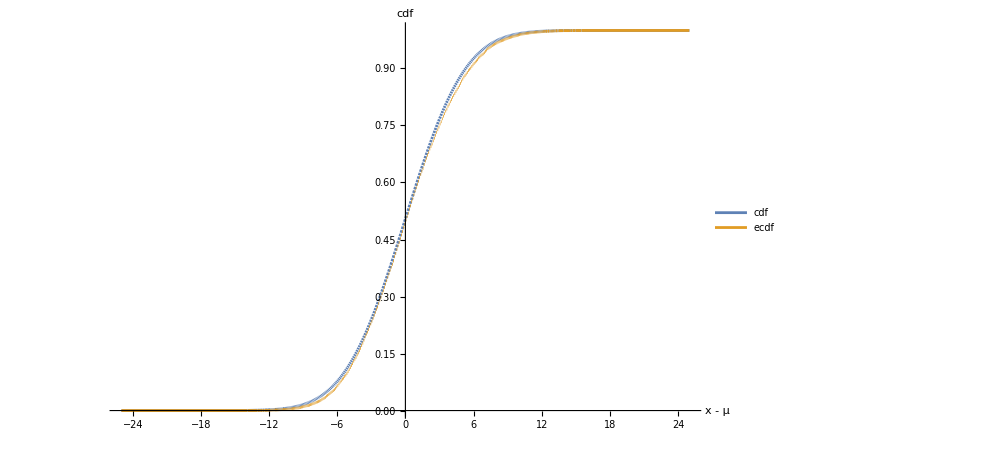

The functions match up well. And using the normally distributed cdf function we get an estimation off p as 0.768893. We can also plot the probability distribution function of the absolute error between the true mean and estimated mean:

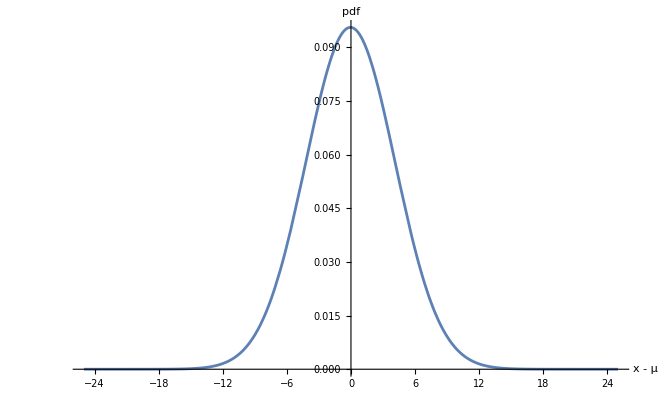

## Code

The sample.

```mathematica
sample = {56,101,78,67,93,87,64,72,80,69};
```

Estimating μ:

```mathematica
μ = N[Mean[sample]]
```

76.7

we Realize p=P(-5< x̄-μ<5) = P(-5+μ<x̄<5+μ)

```mathematica
low=-5+μ
top=5+μ
```

71.7

81.7

we further realize that p=P(low<x̄<top).

Below is a bootstraping function which takes a sample and generates a number of resamples and saves the mean for each resample in a list. The function then returns the sorted list of mean values.

```mathematica
BootStrap[sample_, Nresamples_]:=Module[{n=Nresamples,means={}},
	For[i=1, i<=n, i++,
		randResample = RandomChoice[sample,Length[sample]];
		means = Join[means,{N[Mean[randResample]]}];
	];
	Return[Sort[means]];
];
```

A cdf function of the bootstrap mean distribution.

```mathematica
ecdf[x_,means_]:=N[Sum[If[i<=x,i,0],{i,means}]/Sum[i,{i,means}]];
```

A cdf estimation function based on normaldistribution.

```mathematica
pdf[x_,means_]:=N[PDF[NormalDistribution[Mean[means],StandardDeviation[means]],x]];
```

```mathematica
cdf[x_,means_]:= N[CDF[NormalDistribution[Mean[means], StandardDeviation[means]],x]];
```

We generate a set of means.

```mathematica
nresamples = 10000;
```

```mathematica
means=BootStrap[sample,nresamples];
```

We are interested in estimating p = P(low < x̄ < top) ≈ ecdf(top)-ecdf(low)

```mathematica
p=ecdf[top,means] - ecdf[low,means]
Subscript[p, N]=cdf[top, means] - cdf[low,means]
```

0.761464

0.767091

```mathematica
percentp=Dynamic[PercentForm[p]]
```

We plot the cdf based on the set of means(ecdf) as well as the normal distribution CDF and PDF based on the set of means parameters.

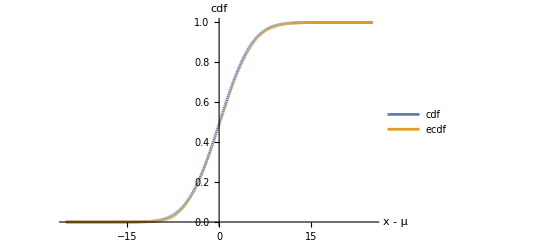

```mathematica
plot0=Plot[{cdf[x+μ,means], ecdf[x+μ,means]}, {x,-25,25},AxesLabel->{"x - μ","cdf"},PlotLegends->{"cdf","ecdf"}]
```

Plotting the pdf of the error rate distribution.

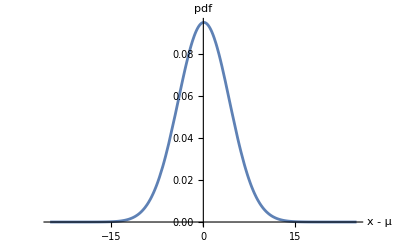

```mathematica
plot1=Plot[pdf[x+μ,means],{x,-25,25}, AxesLabel->{"x - μ","pdf"}]
```